```mathematica
rf[ϕ_]:=rfamplitude Cos[crest Degree-(ϕ +RandomVariate[NormalDistribution[0,$PhaseResolution]])Degree]
```

```mathematica
rf[{ϕ1_,ϕ2_:0,ϕ3_:0,ϕ4_:0,ϕ5_:0,ϕ6_:0}]:=Total[rfamplitude (Cos[#[[2]] Degree-(#[[1]] +RandomVariate[NormalDistribution[0,$PhaseResolution]])Degree]&/@Transpose[{{ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6},crest}])]
```

```mathematica
qe=QuantityMagnitude[UnitConvert[Quantity["ElectronVolt"]]]
```

1.602177×10^-19

```mathematica
c=QuantityMagnitude[UnitConvert[Quantity["SpeedOfLight"]]]
```

299792458

```mathematica
Bρ[p_]:=Evaluate[QuantityMagnitude[UnitConvert[Quantity[p,"eV/c"]/Quantity["ElectronCharge"],"Tesla Meter"]]]
```

```mathematica
dipoleangle[B_,p_:10^6]:=(B dipoleLength)/Bρ[p]
```

```mathematica
finalMomentum[ϕ_]:=If[#<0.1,0.1,#]&[(startingP+rf[ϕ])]
```

```mathematica
bpmPosition[B_,ϕ_]:=Block[{finalmom},
finalmom=finalMomentum[ϕ];
If[#<-10,-10,If[#>10,10,#]]&[Mean[Table[10^3(driftLength*(bpmangle-dipoleangle[B,finalmom]))+RandomVariate[NormalDistribution[0,$BPMResolution]],{$BPMAverages}]]]
]
```

```mathematica
Bρ[20 10^6]
```

0.06671282

## Params

```mathematica
$BPMResolution=0.01;
```

```mathematica
$PhaseResolution=0.25
```

0.25

```mathematica
$BPMAverages=1;
```

```mathematica
crest=167;
```

```mathematica
rfamplitude=20 10^6;
```

```mathematica
dipoleLength=0.2;
```

```mathematica
driftLength=0.2;
```

```mathematica
bpmangle=45Degree;
```

```mathematica
startingP=4.5 10^6;
```

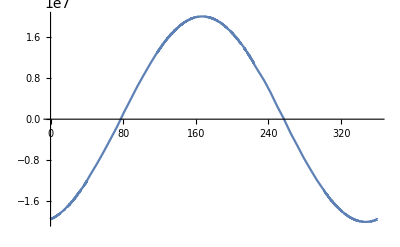

```mathematica
Plot[rf[x],{x,0,360}]
```

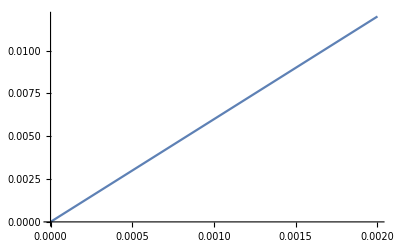

```mathematica
Plot[dipoleangle[B,10 10^6],{B,0,0.002}]
```

```mathematica
bpmPosition[0.3205,crest]
```

0.197323

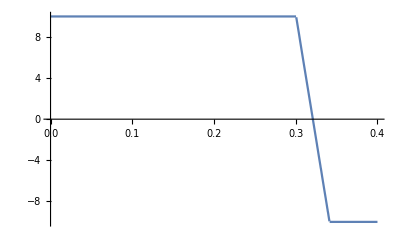

```mathematica
Plot[bpmPosition[B,167],{B,0,0.4}]
```

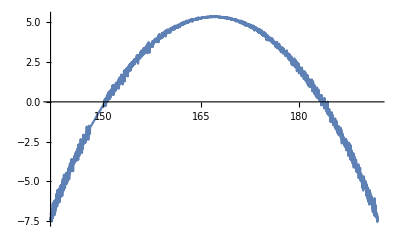

```mathematica
Plot[bpmPosition[0.31,ϕ],{ϕ,crest-25,crest+25}]
```

## Optimiser - 1 Cavity

```mathematica
findStartingPhase[]:=Block[{bpmpos},
phase=0;
B=0.3;
bpmpos=bpmPosition[B,phase];
While[Not[-10<bpmpos<10],
phase+=1;
bpmpos=bpmPosition[B,phase]
];
phase
]
```

```mathematica
crest
```

167

```mathematica
findStartingPhase[]
```

136

```mathematica
findStartingB[phase_]:=Block[{bpmpos},
B=0.3;
bpmpos=bpmPosition[B,phase];
If[bpmpos>1,
While[bpmpos>0,
B+=0.001;
bpmpos=bpmPosition[B,phase]
],
While[bpmpos<0,
B-=0.001;
bpmpos=bpmPosition[B,phase]
]];
bpmpos=bpmPosition[B,phase]
]
```

```mathematica
gradient:=Coefficient[Fit[bpmReadings[[-5;;-1]],{1,fitvar},fitvar],fitvar]
```

```mathematica
Clear[optFunc];
optFunc[phase_Real|phase_Integer]:=Block[{bpmpos},
startbpmpos=bpmpos=bpmPosition[B,phase];
If[bpmpos>0,
While[bpmpos>0,
B+=0.001;
bpmpos=bpmPosition[B,phase]
],
While[bpmpos<0,
B-=0.001;
bpmpos=bpmPosition[B,phase]
]
];
offset+=bpmpos-startbpmpos;
AppendTo[bpmReadings,{phase,bpmpos-offset}][[-1,2]]
]
```

```mathematica
Clear[DoOptimisation];
DoOptimisation[startingPhase_]:=Block[{},
phasesign=+1;
offset=0;
bpmReadings={};
phase=findStartingPhase[];
(*findStartingB[phase];*)
(*Print["BPM = ",phase," B = ",B];*)
Do[phase+=2phasesign;optFunc[phase],{5}];
If[gradient<0,phasesign=-phasesign];
(*Print["Gradient = ",gradient];*)
While[phasesign gradient>-1 ,
phase+=√Max[{1Abs[gradient],0.5}] phasesign;
optFunc[phase]
];
guesscrest=Mod[bpmReadings[[Position[bpmReadings,Max[bpmReadings[[All,2]]]][[1,1]]]][[1]],360];
{crest-guesscrest,
crest-(ϕ/.FindFit[bpmReadings,{fiteq=a+b Cos[ϕ Degree-x Degree],(guesscrest-20)<ϕ<(guesscrest+20)},{a,b,{ϕ,(guesscrest-20)}},x])}
]
```

```mathematica
$BPMResolution=0.1
```

0.1

```mathematica
$BPMAverages=3
```

3

```mathematica
$PhaseResolution=0.1;
```

```mathematica
crest=RandomReal[{0,360}];
DoOptimisation[startingPhase]
```

{3.06799,0.171413}

```mathematica
testdata=Table[crest=RandomReal[{0,360}];
DoOptimisation[startingPhase],{500}];
```

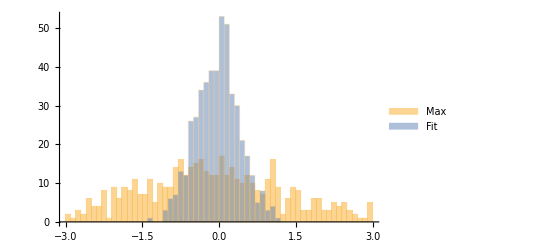

```mathematica
Histogram[Transpose[testdata],{-3,3,0.1},PlotRange->{{-3,3},Automatic},ChartLegends->{"Max","Fit"}]
```

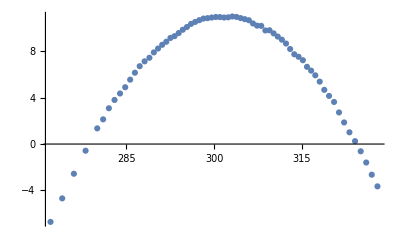

```mathematica
ListPlot[bpmReadings]
```

```mathematica
bpmReadings[[Position[bpmReadings,Max[bpmReadings[[All,2]]]][[1,1]]]]
```

{303.141,10.986}

```mathematica
Length[bpmReadings]
```

67

```mathematica
(fitans=FindFit[bpmReadings,{fiteq=a+b Cos[ϕ Degree-x Degree]^0.5,0<ϕ<360},{a,b,{ϕ,phase}},x])
```

{a→-258.597,b→269.516,ϕ→301.552}

```mathematica
crest
```

301.139

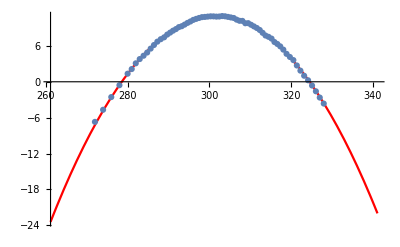

```mathematica
Show[Plot[fiteq/.fitans,{x,crest-40,crest+40},PlotStyle->Red],ListPlot[bpmReadings]]
```

## Optimiser - 6 Cavities

```mathematica
Clear[findStartingPhase];
```

```mathematica
findStartingPhase[n_:1]:=Block[{bpmpos},
bpmpos=bpmPosition[B,phase];
While[Not[-5<bpmpos<5],
phase[[n]]+=1;
bpmpos=bpmPosition[B,phase]
];
phase
]
```

```mathematica
crest
```

167

```mathematica
phase
```

phase

```mathematica
B
```

B

```mathematica
bpmPosition[0.55,{210.46967132444684,62,0,0,0,0}]
```

Transpose::nmtx: The first two levels of {{210.47,62,0,0,0,0},167} cannot be transposed.

Transpose::nmtx: The first two levels of {0.72246,-0.254224,-0.97329,-0.97329,-0.97329,-0.97329} cannot be transposed.

If[0.00765186+200. (45 °-(3.29772×10^7)/If[2.45×10^7+Transpose[{0.72246,-0.254224,-0.97329,-0.97329,-0.97329,-0.97329}]<0.1,0.1,2.45×10^7+Transpose[{0.72246,-0.254224,-0.97329,-0.97329,-0.97329,-0.97329}]])<-10,-10,If[0.00765186+200. (45 °-(3.29772×10^7)/If[2.45×10^7+Transpose[{0.72246,-0.254224,-0.97329,-0.97329,-0.97329,-0.97329}]<0.1,0.1,2.45×10^7+Transpose[{0.72246,-0.254224,-0.97329,-0.97329,-0.97329,-0.97329}]])>10,10,0.00765186+200. (45 °-(3.29772×10^7)/If[2.45×10^7+Transpose[{0.72246,-0.254224,-0.97329,-0.97329,-0.97329,-0.97329}]<0.1,0.1,2.45×10^7+Transpose[{0.72246,-0.254224,-0.97329,-0.97329,-0.97329,-0.97329}]])]]

```mathematica
rfamplitude
```

20000000

```mathematica
findStartingB[phase_]:=Block[{bpmpos},
bpmpos=bpmPosition[B,phase];
If[bpmpos>1,
While[bpmpos>0,
B+=0.001;
bpmpos=bpmPosition[B,phase]
],
While[bpmpos<0,
B-=0.001;
bpmpos=bpmPosition[B,phase]
]];
bpmpos=bpmPosition[B,phase]
]
```

```mathematica
Clear[gradient];
```

```mathematica
gradient[n_]:=Coefficient[Fit[Transpose[{bpmReadings[[All,1,n]],bpmReadings[[All,2]]}][[-5;;-1]],{1,fitvar},fitvar],fitvar]
```

```mathematica
Clear[optFunc];
optFunc[{phase__}]:=Block[{bpmpos},
startbpmpos=bpmpos=bpmPosition[B,{phase}];
If[bpmpos>0,
While[bpmpos>0,
B+=0.001;
bpmpos=bpmPosition[B,{phase}]
],
While[bpmpos<0,
B-=0.001;
bpmpos=bpmPosition[B,{phase}]
]
];
offset+=bpmpos-startbpmpos;
AppendTo[bpmReadings,{{phase},bpmpos-offset,B}][[-1,2]]
]
```

```mathematica
Clear[DoOptimisation];
DoOptimisation[startingPhase_,n_:1]:=Block[{},
rfamplitude[[n]]=20 10^6;
phasesign=+1;
offset=0;
bpmReadings={};
If[n==1,
B=0.2,
B+=Badd
];
phase=findStartingPhase[n];
Do[phase[[n]]+=3phasesign;optFunc[phase],{5}];
If[gradient[n]<0,phasesign=-phasesign];
If[phasesign gradient[n]<1/n,
While[phasesign gradient[n]<1/n,
phase[[n]]+=-√Max[{20 n Abs[gradient[n]],1}] phasesign;
optFunc[phase]
]
];
While[phasesign gradient[n]>-1/n,
phase[[n]]+=√Max[{20 n Abs[gradient[n]],1}] phasesign;
optFunc[phase]
];
guesscrest=Mod[bpmReadings[[Position[bpmReadings,Max[bpmReadings[[All,2]]]][[1,1]]]][[1,n]],360];
B=bpmReadings[[Position[bpmReadings,Max[bpmReadings[[All,2]]]][[1,1]]]][[-1]];
finalcrest=(ϕ/.FindFit[Transpose[{bpmReadings[[All,1,n]],bpmReadings[[All,2]]}],{fiteq=a+b Cos[ϕ Degree-x Degree],(guesscrest-20)<ϕ<(guesscrest+20)},{a,b,{ϕ,(guesscrest)}},x]);
phase[[n]]=finalcrest;
(*Print[Length[bpmReadings]];*)
{crest[[n]]-guesscrest,
crest[[n]]-finalcrest}
]
```

```mathematica
bpmReadings[[Position[bpmReadings,Max[bpmReadings[[All,2]]]][[1,1]]]][[-1]]
```

1.63

```mathematica
crest
```

{152.451,49.0543,203.593,185.952,223.617,242.492}

```mathematica
phase={0,0,0,0,0,0};
```

```mathematica
$BPMResolution=0.01
```

0.01

```mathematica
$BPMAverages=1
```

1

```mathematica
$PhaseResolution=0.001;
```

```mathematica
Badd=0.2
```

0.2

```mathematica
phase=rfamplitude=Table[0,{6}];
crest=RandomReal[{0,360},{6}];
DoOptimisation[phase,#]&/@Range[6]
```

{{-1.0476,0.774984},{-0.87591,-0.00184955},{-0.232055,0.0187704},{0.452639,-0.177942},{1.73427,0.0804447},{-0.764158,-0.185458}}

```mathematica
B
crest-phase
```

1.63

{0.774984,-0.00184955,0.0187704,-0.177942,0.0804447,-0.185458}

```mathematica
testdata=Table[
phase=rfamplitude=Table[0,{6}];
crest=RandomReal[{0,360},{6}];
DoOptimisation[phase,#]&/@Range[6],{50}];
```

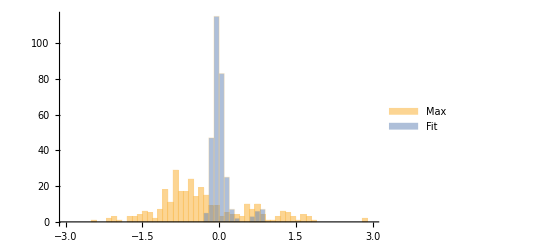

```mathematica
Histogram[Transpose[Flatten[testdata,1]],{-3,3,0.1},PlotRange->{{-3,3},Automatic},ChartLegends->{"Max","Fit"}]
```

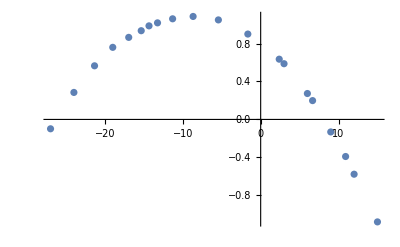

```mathematica
ListPlot[Transpose[{bpmReadings[[All,1,6]],bpmReadings[[All,2]]}]]
```

```mathematica
Length[bpmReadings]
```

20

```mathematica
n=6;
(fitans=FindFit[Transpose[{bpmReadings[[All,1,n]],bpmReadings[[All,2]]}],{fiteq=a+b Cos[(ϕ-x) Degree],(guesscrest-20)<ϕ<(guesscrest+20)},{a,b,{ϕ,(guesscrest)}},x])
```

{a→-23.7173,b→24.8228,ϕ→350.91}

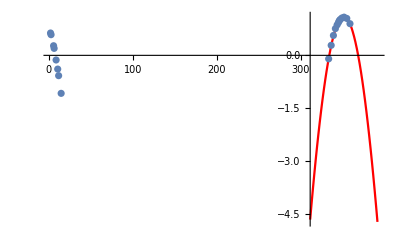

```mathematica
Show[Plot[fiteq/.fitans,{x,crest[[n]]-40,crest[[n]]+40},PlotStyle->Red],ListPlot[Transpose[{Mod[bpmReadings[[All,1,n]],360],bpmReadings[[All,2]]}]],PlotRange->All]
```